# Flow tree formula for quivers

Based on the paper `Attractor flow trees, BPS indices and quivers,’’ by S. Alexandrov and B. Pioline,  arXiv:1804.06928
Updated to CoulombHiggs6.0 in Dec 2020

```mathematica
SetDirectory[NotebookDirectory[]];
<<CoulombHiggs`
```

CoulombHiggs 6.0 - A package for evaluating quiver invariants

## Random examples of Abelian quivers without loop

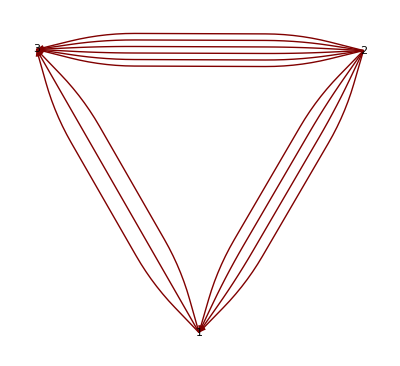

```mathematica
n=3;
Mat=RandomDSZWithNoLoop[n,5];
QuiverPlot[Mat]
```

```mathematica
Nvec=ConstantArray[1,n];
Cvec=RandomFI[Nvec];
IndexHiggs=HiggsBranchFormula[Mat,Cvec,Nvec]
```

-(1-y^8-y^18+y^26)/(y^11 (-1+y^2)^2)

```mathematica
IndexTree=FlowTreeFormula[Mat,Cvec,Nvec]/.{OmAtt[gam_,y_]:>0/;Plus@@gam>1}/.{OmAtt[gam_,y_]:>1}
```

-(1/y^13-1/y^5-y^5+y^13)/(-1/y+y)^2

```mathematica
Simplify[IndexHiggs-IndexTree]
```

0

```mathematica
(* testing non-Abelian case *)
Nvec=Flatten[{ConstantArray[1,n-1],2}];
Cvec=RandomFI[Nvec];
IndexHiggs=HiggsBranchFormula[Mat,Cvec,Nvec]
```

-(-1+y^6+y^32-y^38+(-1+y^2)/(-1+y^4)-(y^12 (-1+y^2))/(-1+y^4)-(y^32 (-1+y^2))/(-1+y^4)+(y^44 (-1+y^2))/(-1+y^4))/(y^19 (-1+y^2)^3)

```mathematica
IndexTree=FlowTreeFormula[Mat,Cvec,Nvec]/.{OmAtt[gam_,y_]:>0/;Plus@@gam>1}/.{OmAtt[gam_,y_]:>1}
```

(1/y^22-1/y^10-y^10+y^22)/(2 (-1/y+y) (-1/y^2+y^2))-(-1/y^22+2/y^16-1/y^10+y^10-2 y^16+y^22)/(2 (-1/y+y)^3)

FlowTreeFormula: Constructing Poincaré polynomial...

(1/y^14-1/y^10-y^10+y^14)/(2 (-1/y+y) (-1/y^2+y^2))-(-1/y^14+1/y^10+2/y^2-2 y^2-y^10+y^14)/(2 (-1/y+y)^3)

```mathematica
Simplify[IndexHiggs-IndexTree]
```

0

## Random examples of Abelian quivers with loop

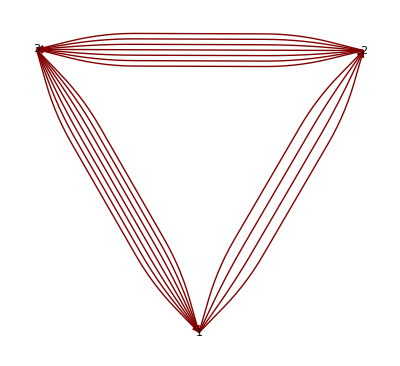

```mathematica
n=3;
Mat=RandomDSZWithLoop[n,5];
QuiverPlot[Mat]
```

```mathematica
Nvec=ConstantArray[1,n];
Cvec=RandomFI[Nvec];
IndexCoulomb=CoulombBranchFormula[Mat,Cvec,Nvec]
```

-(2 y^2)/((-1+y^2)^2)+(1/y^4+y^4)/(-1/y+y)^2+OmS[{1,1,1},y,t]

```mathematica
IndexTree=FlowTreeFormula[Mat,Cvec,Nvec]
```

OmAtt[{1,1,1},y]

```mathematica
IndexTreeQ=IndexTree/.{OmAtt[gam_,y_]:>1/;Plus@@gam==1,OmAtt[gam_,y_]:>0/;Plus@@gam==2}
```

OmAtt[{1,1,1},y]

```mathematica
Simplify[IndexTreeQ-IndexCoulomb]
```

-((1+y^2)^2)/y^2+OmAtt[{1,1,1},y]-OmS[{1,1,1},y,t]

## Comparing various schemes for evaluating the partial tree index

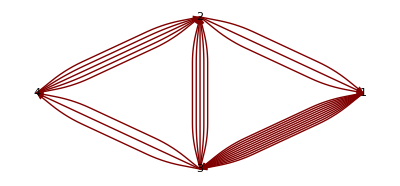

```mathematica
n=4;Mat=RandomDSZWithLoop[n,5];
QuiverPlot[Mat]
```

```mathematica
RMat=Table[Random[Integer,{1,100000}],{i,n},{j,n}];
RMat=1/100000/$QuiverPerturb1 Table[Which[i<j,RMat[[i,j]],i>j,-RMat[[j,i]],i==j,0],{i,n},{j,n}];
PMat=Mat+RMat;
```

```mathematica
{a1,a2,a3}={0,0,0};
Monitor[While[a1==a2 &&a2==a3,
Cvec=Table[Random[Integer,{-10000,10000}],{i,n}]/10000;
Cvec[[n]]=-Sum[Cvec[[i]],{i,n-1}];{a1,a2,a3}={TreeF[PMat,Cvec],TreeFAlt1[PMat,Cvec],TreeFAlt2[PMat,Cvec]};],{a1,a2,a3}]
```

$Aborted